# Temp

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Clothilde\Documents\GitHub\hyperion-console\build\Release

## Functions

#### Read input file Functions

```mathematica
readFile[fileName_]:=Module[{str,i,j,aimingpoint,latitudeDegree,βatm,I0atm,attenuationModel,nreceivers,receiversRadius,efficiencyType,efficiencyMatrix},
str = OpenRead[fileName, BinaryFormat->True];
latitudeDegree = BinaryRead[str, "Real64", ByteOrdering->-1]/Degree;
βatm = BinaryRead[str, "Real64", ByteOrdering->-1];
I0atm = BinaryRead[str, "Real64", ByteOrdering->-1];
attenuationModel = BinaryRead[str, "TerminatedString",  ByteOrdering->-1];
nreceivers=BinaryRead[str, "Integer32", ByteOrdering->-1];
aimingPoints={};
receiversRadius={};
For[i=1,i≤nreceivers,i++,
aimingpoint={};
For[j=1,j≤3,j++,
AppendTo[aimingpoint,BinaryRead[str, "Real64", ByteOrdering->-1]];
];
AppendTo[aimingPoints,aimingpoint];
AppendTo[receiversRadius,BinaryRead[str, "Real64", ByteOrdering->-1]];
];
nrows = BinaryRead[str, "Integer32", ByteOrdering->-1];
ncolumns = BinaryRead[str, "Integer32", ByteOrdering->-1];
xmin = BinaryRead[str, "Real64", ByteOrdering->-1];
xmax = BinaryRead[str, "Real64", ByteOrdering->-1];
ymin = BinaryRead[str, "Real64", ByteOrdering->-1];
ymax = BinaryRead[str, "Real64", ByteOrdering->-1];
efficiencyType = BinaryRead[str, "TerminatedString",  ByteOrdering->-1];
efficiencyList= BinaryReadList[str, "Real64", ByteOrdering->-1];
Close[str];
]
```

```mathematica
partitionList[]:=Module[{temp,efficiencyMatrix},
temp=Partition[efficiencyList, ncolumns]; 
If[xmax==0. (* Add the West symmetry *),
efficiencyMatrix=Table[If[j≤ncolumns,temp[[i]][[j]],temp[[i]][[2*ncolumns-j+1]]],{i,1,nrows},{j,1,2 *ncolumns}];
xmax=Abs[xmin];
ncolumns*=2;
efficiencyList=Flatten[efficiencyMatrix];
Clear[temp],
If[xmin==0. (* Add the East symmetry *), 
temp=Partition[efficiencyList, ncolumns]; 
efficiencyMatrix= Table[If[j≤ncolumns,temp[[i]][[ncolumns-j+1]],temp[[i]][[j-ncolumns]]],{i,1,nrows},{j,1,2 *ncolumns}];
xmin=-Abs[xmax];
ncolumns*=2;
efficiencyList=Flatten[efficiencyMatrix];
Clear[temp],
(* No symmetry needed *)
efficiencyMatrix = Partition[efficiencyList, ncolumns]
];];
Return[efficiencyMatrix];
]
```

#### Mean efficiency of all field sizes and tower heights for a given latitude for cos or cos+att only

```mathematica
meanEfficiencyList[]:=Module[{temp,ncells,cellSize,maxCells,ans},
ncells=Table[Round[fieldSizeList[[i]]*1000000./cellSize],{i,1,Length@fieldSizeList}];
cellSize=(ymax-ymin)/nrows*(xmax-xmin)/ncolumns;
maxCells=nrows*ncolumns;
If[ncells<maxCells,Print["Not enough cells"]];
temp=Sort[efficiencyList,Greater];
ans=Table[Mean[temp[[1;;ncells[[i]]]]],{i,1,Length@fieldSizeList}];
Return[ans]
]
```

```mathematica
meanEfficiencyLoop[efficiencyType_,latitude_]:=Module[{filenames,meanList,i,filename,list},
filenames=FileNames["Efficiency-"<>efficiencyType<>"_Lat-"<>latitude<>"_TH*_Resolution-5x5.dat"];
meanList={};
For[i = 1, i≤ Length[filenames],i++, 
filename =filenames[[i]];
readFile[filename];
partitionList[];
list=meanEfficiencyList[];
PrependTo[list,aimingPoints[[1,-1]]];
AppendTo[meanList,list]
];
meanList=Prepend[Sort[meanList],Prepend[fieldSizeList,"TH \ Field size"]];
Clear[ymax,ymin,nrows,xmax,xmin,ncolumns];
Return[meanList]
]
```

#### Functions for Plots

```mathematica
typeEfficiency[e_] :=Switch[e,
"Cos",rangeLat={{0.,1000.},{70,91}};(*rangeFS={0.75,0.92}*)rangeFS={{0.,1000.},{80,91.1}};pos={50,0.91};,
"CosAtt",rangeFS={{0.,1000.},{65,87}};rangeLat={{0.,1000.},{65,82}};(*rangeFS={68,87}*)pos={50,0.854};,
"AllFactors",rangeLat=rangeFS={{0.,1000.},{70,87}};(*rangeFS={68,87}*)pos={50,0.854};
]
```

```mathematica
legends[e_]:=Module[{},
(* All Plots *)
typeEfficiency[e]; 
label={"Tower Height (m)","Mean Annual Efficiency (%)"};
(* Field Size Plot *)
linelegendFS=Table[ToString[DecimalForm[fieldSizeList[[j]]],FormatType->StandardForm],{j,1,Length@fieldSizeList}];
colorDataFS=Table[ColorData["Rainbow",i/(Length[fieldSizeList]-1)],{i,0,Length[fieldSizeList]-1}];
labelLegendFS=Row@{Style["Field Size (",10,FontFamily->"Arial"],Spacer[1],Style[Superscript[km,2],10,ScriptMinSize->6,"Text",FontFamily->"Arial"],Spacer[1],Style[")",10,FontFamily->"Amienne"]};
(* Latitude Plot *)
linelegendLat={"0","10","20","30","40","50","60"};
colorDataLat=Table[ColorData["DarkRainbow",i/(Length[linelegendLat]-1)],{i,0,Length[linelegendLat]-1}];
labelLegendLat="Latitude (°)";
]
```

```mathematica
findOptimum[efficiencyList_]:=Module[{function,temp},
function=Interpolation[efficiencyList];
temp=FindMaximum[function[x],{x,20,1000}];
Return[{temp[[2,1,2]],temp[[1]]}]
]
```

```mathematica
plotsData[filename_,e_,latitude_,FieldSize_]:=Module[{efficiencyMatrix,temp},
legends[e];
efficiencyMatrix=Import[filename<>e<>"_AllFieldSizes_Lat-"<>latitude<>".csv"][[2;;-1]];
efficiencyMatrix[[All,2;;-1]]*=100;
listPlotFS=Table[Transpose[Join[{efficiencyMatrix[[All,1]],efficiencyMatrix[[All,j+1]]}]],{j,1,Length@fieldSizeList}];
If[e=="Cos",optPtsFS={},
optPtsFS=Table[{PointSize[Medium],colorDataFS[[i]],Point[findOptimum[listPlotFS[[i]]]]},{i,1,Length@listPlotFS}];
];
efficiencyMatrix=Import[filename<>e<>"_AllLatitudes_FieldSize-"<>FieldSize<>".csv"][[2;;-1]];
efficiencyMatrix[[All,2;;-1]]*=100;
listPlotLat=Table[Transpose[Join[{efficiencyMatrix[[All,1]],efficiencyMatrix[[All,j]]}]],{j,2,8}];
If[e=="Cos",optPtsLat={},
optPtsLat=Table[{PointSize[Medium],colorDataLat[[i]],Point[findOptimum[listPlotLat[[i]]]]},{i,1,Length@listPlotLat}];
];
]
```

## Use

#### Export Mean efficiencies fct of TH and FS for a given latitude and efficiency type

```mathematica
efficiencytype="CosAtt"
latitude="0"
fieldSizeList=Table[i,{i,0.1,2.5,0.2}]; (* km2 *)
matrix=meanEfficiencyLoop[efficiencytype,latitude];
Export["MeanEfficiencyVSTowerHeight_"<>efficiencytype<>"_AllFieldSizes_Lat-"<>latitude<>".csv",matrix]
```

CosAtt

0

MeanEfficiencyVSTowerHeight_CosAtt_AllFieldSizes_Lat-0.csv

#### Import file for graphs: per Lat & per TH

```mathematica
efficiencytype="Cos";
fieldSizeList= Table[i,{i,0.1,2.5,0.2}]; (* km2 *)
latitude="30";
fieldSize="1.3km2";
plotsData["MeanEfficiencyVSTowerHeight_",efficiencytype,latitude,fieldSize]
```

Graphs with Field Size

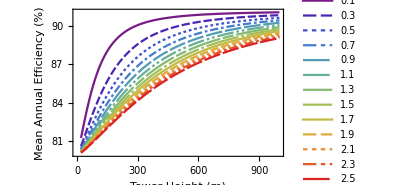

```mathematica
imageFieldSize=ListPlot[listPlotFS,Joined->True,InterpolationOrder->2,PlotTheme->{"Monochrome"},PlotMarkers->None,PlotStyle->colorDataFS,Frame->True,PlotRange->rangeFS,
FrameLabel->label,LabelStyle->{FontFamily->"Arial",10,GrayLevel[0]},PlotLegends->Placed[LineLegend[linelegendFS,Spacings->0.5,LegendMarkerSize->{20,1},LegendLayout->{"Column",3},LegendLabel->labelLegendFS],{0.72,0.32}],ImageSize->{300,200},Epilog->optPtsFS]
```

```mathematica
Export["EfficencyVsTH_FieldSizes_Lat30_"<>efficiencytype<>".png",imageFieldSize,ImageResolution->500]
```

EfficencyVsTH_FieldSizes_Lat30_Cos.png

Graphs with Latitude

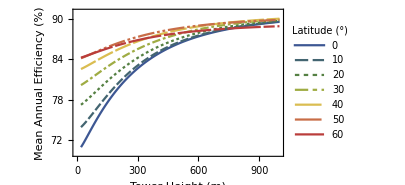

```mathematica
imageLat=ListPlot[listPlotLat,Joined->True,InterpolationOrder->2,Frame->True,
PlotTheme->{"Monochrome"},PlotMarkers->None,PlotStyle->colorDataLat,PlotRange->rangeLat,FrameLabel->label,(*GridLines->{{{100.,Gray}},{0}},*)LabelStyle->{FontFamily->"Arial",10,GrayLevel[0]},
PlotLegends->Placed[LineLegend[linelegendLat,LegendMarkerSize->{22,1},LegendLayout->{"Column",2},LegendLabel->labelLegendLat],{0.55,0.3}],ImageSize->{300,200},Epilog->optPtsLat]
```

```mathematica
Export["EfficencyVsTH_Latitudes_"<>efficiencytype<>".png",imageLat,ImageResolution->400]
```

EfficencyVsTH_Latitudes_Cos.png

#### Efficiency map per field size for boundary check

```mathematica
filename="Efficiency-AllFactors_Lat-0_TH-1000_RecRadius-13_Resolution-5x5.dat";
readFile[filename];
efficiencyMatrix=partitionList[];
```

```mathematica
fieldSize=2500000.;
cellSize=(ymax-ymin)/nrows*(xmax-xmin)/ncolumns
ncells=Round[fieldSize/cellSize];
```

25.

```mathematica
(*If[ncells<maxCells,*)
temp=Sort[efficiencyList,Greater];
Mean[temp[[1;;ncells]]]
max=temp[[ncells]]
```

0.785163

0.754075

```mathematica
fieldMatrix=Table[If[efficiencyMatrix[[i]][[j]]≥ max,efficiencyMatrix[[i]][[j]],0.],{i,1,nrows},{j,1,ncolumns}];
```

```mathematica
plotFieldSize=ArrayPlot[Reverse[fieldMatrix],DataRange->{{xmin, xmax},{ymin,ymax}},GridLines->{{-1000.,1000.},{3000.}},FrameTicks->{{Range[ymin,ymax,200],None},{Automatic,None}},FrameTicksStyle->Directive[Black,12],PlotRange->{max,1.}, ColorFunction->"Rainbow",Background->White, PlotLegends->Automatic]
```

-Graphics-

```mathematica
Export[filename<>"_FieldSize-2.5km2.jpg",plotFieldSize]
```

Efficiency-AllFactors_Lat-0_TH-500_RecRadius-5_Resolution-5x5_FieldSize-2.5km2.jpg

#### Efficiency map

```mathematica
ArrayPlot[efficiencyMatrix, DataReversed->True, ColorFunction->"Rainbow", PlotLegends->Automatic]
```

```mathematica
ListContourPlot[efficiencyMatrix, DataRange->{{xmin, xmax},{ymin,ymax}},ColorFunction->"Rainbow",RegionFunction->(#>max&), PlotLegends->Automatic]
```

```mathematica
(* ListDensityPlot[efficiencyMatrix, DataRange->{{xmin, xmax},{ymin,ymax}}, ColorFunction->"Rainbow",PlotLegends->Automatic] *)
```